{{-5,18816},{-4,4860},{-3,800},{-2,48},{-1,0},{0,-4},{1,0},{2,0},{3,128},{4,1500}}

-5. | 18816.
-4. | 4860.
-3. | 800.
-2. | 48.
-1. | 0.
0. | -4.
1. | 0.
2. | 0.
3. | 128.
4. | 1500.

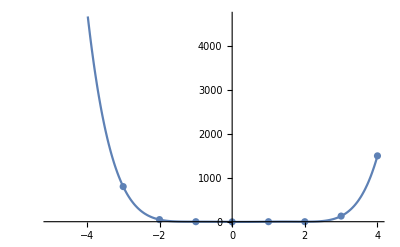

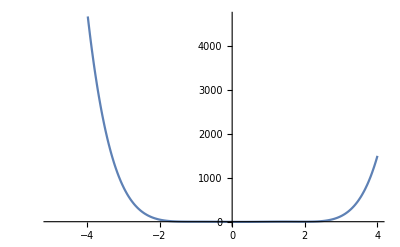

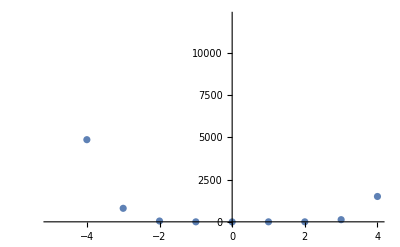

```mathematica
xmin = -5;
xmax = 4;
n  = 10;
h = (xmax - xmin) / (n - 1);
f[x_]:=x^6-2x^5-4x^4+6x^3+7x^2-4x-4
table1 = Table[{x = xmin+i×h, f[x]},{i,0,n-1}]
table1 = TableForm[N[table1]]
gr1 := Plot[f[x],{x,xmin,xmax}]
gr2:=ListPlot[{{-5,18816},{-4,4860},{-3,800},{-2,48},{-1,0},{0,-4},{1,0},{2,0},{3,128},{4,1500}}]
Show[{gr1,gr2}]
Show[{gr1}]
Show[{gr2}]
```